# Portfolio Optimization with the Quantum Approximate Optimization Algorithm (QAOA)

## Introduction

The [1] and [2] links don’t work for me.
Mads: revised

Portfolio optimization [1] is the process of allocating a portfolio of financial assets optimally, according to some predetermined goal. Usually, the goal is to maximize the potential return while minimizing the financial risk of the portfolio. One can express this problem as a combinatorial optimization problem like many other real-world problems. In this demo, we’ll show how the Quantum Approximate Optimization Algorithm (QAOA) [2] can be employed on the Classiq platform to solve the problem of portfolio optimization.

### "Modeling the Portfolio Optimization Problem"

As a first step, we have to model the problem mathematically. We will use a simple yet powerful model, which captures the essence of portfolio optimization:

A portfolio is built from a pool of  financial assets, each asset labeled .

Every asset’s return is a random variable, with expected value  and variance  (modeling the financial risk involved in the asset).

Every two assets  have covariance  (modeling market correlation between assets).

Every asset  has a weight  in the portfolio, with b_i defined as the budget for asset  (modeling the maximum allowed weight of the asset).

The return vector , the covariance matrix  and the weight vector  are defined naturally from the above (with the domain  for ).

With the above definitions, the total expected return of the portfolio is , and the total risk is . We’ll use a simple difference of the two as our cost function, with the additional constraint that the total sum of assets does not exceed a predefined budget . We note that there are many other possibilities for defining a cost function (e.g. add a scaling factor to the risk/return or even some nonlinear relation). For reasons of simplicity, we select the model below, and we assume all constants and variables are dimensionless. Thus, the problem is, given the constant inputs , to find the optimal variable  as follows:

subject to

or subject to

The case presented above is called integer portfolio optimization, since the domains D_i are over the (positive) integers. Another variation of this problem defines weights over binary domains and will not be discussed here.

The code in the following section is incomplete, with missing parts that you need to fill in, indicated by “#TODO” in the code description. If you’re unsure how to use a specific Classiq function, please refer to the Classiq documentation and search for the required quantum function to find its corresponding documentation page.

The solution is here to help you in between the SOLUTIONSTART and SOLUTIONEND.

### Classiq Setup

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
<<Wolfram`QuantumFramework`
<<Wolfram`QuantumFramework`QuantumOptimization`
```

PacletObject[…]

```mathematica
classiq=ClassiqSetup[{"Session","ClassiqVersion"},"CheckDependencies"->{"pyomo"}]
```

Installing latest Classiq version

```mathematica
session=classiq["Session"]
```

ExternalSessionObject[…]

#### Register an Account with Classiq

In order to authenticate with the Classiq servers, you will need to follow Classiq's registration instructions, and be logged in to https://platform.classiq.io.

This takes less than five minutes. Much of Classiq’s library can be used without registration. However, the circuit synthesis and state vector simulation for a very large circuit will require this registration and authentication step.

Authenticate (the device can only be authenticated once; a warning is shown when trying twice):

from classiq import authenticate
authenticate()

## The Portfolio Optimization Problem Parameters

First we define the parameters of the optimization problem, which include the expected return vector, the covariance matrix and the total budget:

import numpy as np
import pyomo.core as pyo

returns = np.array([3, 4, -1])
covariances = np.array(
    [
        [0.9, 0.5, -0.7],
        [0.5, 0.9, -0.2],
        [-0.7, -0.2, 0.9],
    ]
)

total_budget = 6

### The Pyomo Model for the Problem

First we define the optimization problem using the Pyomo package. Note that there is an alternative formulation using QMOD only, which is natural for QMOD developers and is available for you to use. However, we will use the Pyomo package to define the problem, as it is more common in the optimization community:

# Define the Pyomo model for the portfolio optimization problem
portfolio_model = pyo.ConcreteModel("portfolio_optimization")

# Define the number of assets
num_assets = len(returns)

# Define integer decision variables (weights of assets). Note that the weights are integers between 0 and 7.
portfolio_model.w = pyo.Var(range(num_assets), domain=pyo.Integers, bounds=(0, 7))

w_array = list(portfolio_model.w.values())

# Penalty term: Budget constraint, we can use equality or inequality constraint
portfolio_model.budget_rule = pyo.Constraint(
    expr=sum(portfolio_model.w[i] for i in range(num_assets)) == total_budget
)

# Expected return: μ^T w, where μ is the expected return vector and w is the weight vector.
portfolio_model.expected_return = returns @ w_array

# Risk term: w^T Σ w where Σ is the covariance matrix.
portfolio_model.risk = w_array @ covariances @ w_array


# Objective function (minimize risk - expected return)
portfolio_model.cost = pyo.Objective(
    expr=portfolio_model.risk - portfolio_model.expected_return, sense=pyo.minimize
)

### Setting Up the Classiq Problem Instance

In order to solve the Pyomo model defined above, we use the pyo_model_to_hamiltonian function to convert the Pyomo model to a Hamiltonian, which is the actual thing we are minimizing in the QAOA algorithm. In this tutorial, it is actually not needed, as we apply the phase from the cost function directly.

We also use the pyo_model_to_qmod_problem function to convert the Pyomo model to a QMOD problem. The Hamiltonian and the QMOD problem are then used to define the QAOA circuit.

#### "Obtaining the Hamiltonian and QMOD Problem"

from classiq.applications.combinatorial_optimization import pyo_model_to_hamiltonian
from classiq.applications.combinatorial_helpers.combinatorial_problem_utils import (
    pyo_model_to_qmod_problem
)

# Penalty energy for the constraints part
penalty_energy = 0.15

# Note that the penalty is a sensitive term. At this point, we may print the Hamiltonian and observe it.
# *** Note that this step is not mandatory ***
problem_hamiltonian = pyo_model_to_hamiltonian(
    pyo_model=portfolio_model,
    penalty_energy=penalty_energy
)

# Next, we convert the Pyomo model to a QMOD problem. This is required to define the QAOA circuit.
QAOA_vars, cost_func = pyo_model_to_qmod_problem(
    pyo_model=portfolio_model,
    penalty_energy=penalty_energy
)

#### Main

To build the “main” function, we will use the Classiq “phase” operator to apply the cost function and the “apply_to_all” operator to apply the mixer Hamiltonian.

responsible to span->responsible for spanning?
Mads: revised according

The mixer Hamiltonian is defined as , where X_i is the Pauli-X operator acting on the i^th qubit. It is responsible for spanning the entire space where we are searching for the optimal solution by creating superposition of 0 and 1 for each qubit, with a parametric weight between them.

The phase layer is applied on each quantum state of the Hilbert space—a phase that is proportional to the cost function applied on that state.

The QAOA circuit is built by applying the cost Hamiltonian and the mixer Hamiltonian alternately for a number of layers. The number of layers is a hyperparameter that can be tuned to improve the performance of the QAOA algorithm. A higher number of layers allows us to explore a more complicated search space and relation between qubits that are not directly related in the resulting Hamiltonian.

Please refer to the documentation to learn more about:

repeat

hadamard_transform

phase

apply_to _all

Atomic gates

from classiq import *
num_layers=4

# Below we define "main" which is the entry point of the QMOD solution.

@qfunc
def main(
    params: CArray[CReal, num_layers * 2],
    vars_reg: Output[QAOA_vars]
) -> None:
    allocate(
        num_qubits = vars_reg.size,
        out = vars_reg
    )

    #TODO: (20 minutes)
    # * Apply Hadamard transform to the qubits in `vars_reg`,
    # * then use repeat to apply the cost and mixer Hamiltonians for num_layers using the phase operation.


    ### your code here ###


    # ========== Solution Start ==========
    hadamard_transform(vars_reg)
    repeat(
        count=num_layers,
        iteration = lambda i: [
            # Cost Hamiltonian
            phase(phase_expr = -cost_func(vars_reg), theta = params[i]),
            # Mixer Hamiltonian
            apply_to_all(lambda q: RX(params[num_layers + i], q), vars_reg)
        ]
    )
        # ========== Solution end ==========

ExternalFunction[…]

#### Create and Write the Model

Refer to the documentation to learn more about create_model:

#TODO: Create the QMOD model using the main function defined above (5 minutes).

### your code here ###

# ========== Solution Start ==========
qmod = create_model(
    entry_point=main
)

# save the QMOD model:
write_qmod(qmod, "portfolio_optimization")

# ========== Solution end ==========

### Synthesizing the QAOA Circuit and Solving the Problem

We can now synthesize and view the QAOA circuit (ansatz) used to solve the optimization problem:

qprog = synthesize(qmod)
show(qprog)

Quantum program link: https://platform.classiq.io/circuit/361bkPhKDCn13UimmlmkQmo2xj2

-Graphics-

We also set the quantum backend we want to execute on and the number of shots for the quantum program. Please refer to the documentation to learn more about ExecutionPreferences:

from classiq.execution import *

execution_preferences = ExecutionPreferences(
    num_shots = 2000,
    backend_preferences=ClassiqBackendPreferences(backend_name="simulator"),
)

[3] link doesn’t work for me.
Mads: revised according

We now solve the problem by calling the optimize method of the Scipy package. First we define the ExecutionSession object that defines the measurement and the execution from the quantum program. Then, for the classical optimization part of the QAOA algorithm, we define the maximum number of classical iterations (maxiter) and the -parameter (quantile) for running CVaR-QAOA, an improved variation of the QAOA algorithm [3].

In this example, we measure and compute the cost classically after sampling the quantum circuit.

#### Define the ExecutionSession Object

ExecutionSession: The object that defines the execution from the quantum program. (see ExecutionSession documentation):

# Define the ExecutionSession object:

#TODO: Define the ExecutionSession object (5 minutes).

### your code here ###


# ========== Solution Start ==========
ES = ExecutionSession(
    quantum_program = qprog, execution_preferences = execution_preferences
)
params_trace = []
cost_trace = []
# ========== Solution end ==========


def classical_cost_function(state) -> float:
    return cost_func(state["vars_reg"])

#TODO: Write the cost function to estimate the cost classically after sampling the quantum circuit (10 minutes).

def estimate_cost_func(params: np.ndarray) -> float:

   # See the execution session documentation for more information on the `estimate_code` method and implement below.

   ### your code here ###

    # ========== Solution Start ==========
    cost = ES.estimate_cost(
        classical_cost_function,
        {"params": params.tolist()},
        quantile=1.0,
    )
        
   # ========== Solution end ==========

    cost_trace.append(cost)
    params_trace.append(params)
    return cost
	
initial_params = np.concatenate(
    (
        np.linspace(1 / num_layers, 1, num_layers),
        np.linspace(1, 1 / num_layers, num_layers),
    )
)

# Run the classical optimization using the Scipy package.
# The optimization results will be stored in the `optimization_results` variable.

from scipy.optimize import minimize

optimization_results = minimize(
    fun = estimate_cost_func,
    x0 = initial_params,
    method="COBYLA",
    options={"maxiter": 80,"rhobeg": 0.5},
)

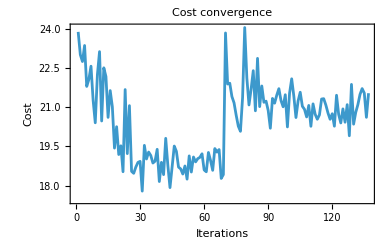

```mathematica
ListLinePlot[ExternalValue[session,"cost_trace"],Frame->True,"PlotLabel"->"Cost convergence",FrameLabel->{"Iterations","Cost"}]
```

### Homework: Explore the Parameter Space, e.g. by Varying the Following:

1. Use equality/inequality constraints.
2. Put more/fewer layers.
3. Change the data.

Or any other idea you have in mind!

## Optimization Results

We can also examine the statistics of the algorithm. The optimization is always defined as a minimization problem, so the positive maximization objective was translated to a negative minimization one by the Pyomo to qmod translator.

In order to get samples with the optimized parameters, we call the sample method:

res = ES.sample(
    {"params": optimization_results.x.tolist()}
)

parsed_result = [
    {
        "solution": {
            key: value
            for key, value in sampled.state["vars_reg"].items()
        },
        "probability": sampled.shots / res.num_shots,
        "cost": cost_func(sampled.state["vars_reg"]),
    }
    for sampled in res.parsed_counts
]

import pandas as pd
optimization_result = pd.DataFrame.from_records(parsed_result)
optimization_result.sort_values(by="cost").head(10)

best_solution = optimization_result.loc[optimization_result.cost.idxmin()]
print(
    "x =",
    best_solution.solution["w"],
    ", cost =",
    best_solution.cost,
)

x = [3, 1, 2] , cost = -4.6

## References

[1] “Portfolio Optimization” (Wikipedia).

[2] Farhi, Edward, Jeffrey Goldstone, and Sam Gutmann. “A Quantum Approximate Optimization Algorithm.” arXiv preprint arXiv:1411.4028 (2014).

[3] Barkoutsos, Panagiotis Kl, et al. “Improving Variational Quantum Optimization Using CVaR.” Quantum 4 (2020): 256.